```mathematica
ClearAll["Global`*"]
```

## Model

```mathematica
f1[x_]:=If[Im[w1*x^2+w2*x+w3]==0,w1*x^2+w2*x+w3,10^11];
```

## Data

```mathematica
xdata=Table[i,{i,1,6,1}];
ydata=Map[f1,xdata]/.{w1->1,w2->2,w3->3};
(*ydataAdjusted=Table[ydata[[i]]+RandomReal[{-15,15}],{i,1,Length[ydata]}];*)
ydataAdjusted={13,14,16,20,21,23};
dataMaker[x_,y_]:=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
expData=dataMaker[xdata,ydata];
expDataAdjusted=dataMaker[xdata,ydataAdjusted];(*
ListPlot[{expData,expDataAdjusted},Joined->{True, True},PlotMarkers->Automatic,Frame->True,Axes->False,AspectRatio->0.8,PlotLegends->Placed[{"Exp.","Exp-Adjusted."},{0.2,0.8}]]*)
```

## Non-Linear Model Fit

```mathematica
nlm=NonlinearModelFit[expDataAdjusted,f1[x],{w1,w2,w3},x];
params=nlm["ParameterTable"]
variance=nlm["EstimatedVariance"]
```

| Estimate | Standard Error | t-Statistic | P-Value
w1 | 0.0178571 | 0.148333 | 0.120386 | 0.911788
w2 | 2.01786 | 1.06069 | 1.9024 | 0.153269
w3 | 10.5 | 1.62129 | 6.47634 | 0.00747151

0.821429

## Parameters

```mathematica
unpack[pars_]:=Table[params[[1,1,i]][[2]],{i,2,4,1}];
pset=unpack[params];
```

## Fitting data

```mathematica
thData=Map[f1,xdata]/.{w1->pset[[1]],w2->pset[[2]],w3->pset[[3]]};
FitResults=dataMaker[xdata,thData];
```

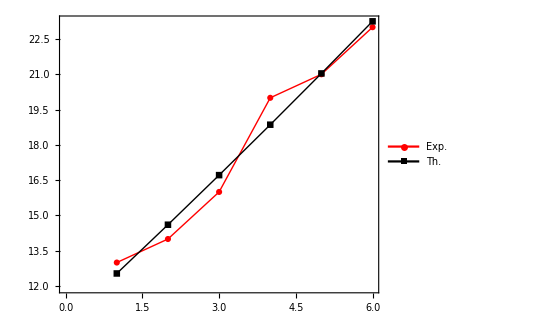

```mathematica
ListPlot[{expDataAdjusted,FitResults},Joined->{True, True},PlotMarkers->{Automatic},Frame->True,Axes->False,AspectRatio->0.8,PlotLegends->Placed[{"Exp.","Th."},{0.2,0.8}],PlotLegends->Full,PlotStyle->{{Red,Thick},{Black,Thick}}]
```